```mathematica
SetDirectory[NotebookDirectory[]];
```

## Energy loss

### Pure AdS energy loss

#### The indeterminate solution to the null geodesic equation in AdS5 is

```mathematica
xGeoInd[z_]:=zH^2/z Hypergeometric2F1[1/4,1/2,5/4,zs^4/z^4];
```

#### As one can easily verify:

```mathematica
Assuming[z>0,Simplify[xGeoInd'[z]]]
```

-zH^2/(√(z^4-zs^4))

#### Assuming that at z=z0, x=0, we have:

```mathematica
xGeoSol[z_]=xGeoInd[z]-xGeoInd[z0]
```

(zH^2 Hypergeometric2F1[1/4,1/2,5/4,zs^4/z^4])/z-(zH^2 Hypergeometric2F1[1/4,1/2,5/4,zs^4/z0^4])/z0

#### Expand for small z*

```mathematica
Series[xGeoSol[z],{zs,0,4}]
```

(zH^2/z-zH^2/z0)+(zH^2/(10 z^5)-zH^2/(10 z0^5)) zs^4+O[zs]^5

#### Energy loss in GeV and fm and for a dimensionless z0

```mathematica
Clear[z0];
hc=0.197;
```

```mathematica
dEdxCFT[x_,T_]:=1/hc*π/2*√λ*T^2*(1/z0+(π*T*x)/hc)^2
```

### Gauss-Bonnet energy loss - derivation

#### AdS5-Schwarzschild with Gauss-Bonnet

ds^2=L^2/z^2(-a^2 f_GB(z)dt^2+dx^2+dz^2/(f_GB(z)))

#### Metric elements:

```mathematica
Clear[λGB];
```

```mathematica
f[z_]:=1-z^4/zH^4;
fGB[z_]:=1/(2λGB)(1-√(1-4λGB f[z]));
a=√(1/2(1+√(1-4λGB)));
```

#### For λGB->0, we get AdS-Sch

```mathematica
Series[fGB[z],{λGB,0,0}]
Series[a,{λGB,0,0}]
```

(1-z^4/zH^4)+O[λGB]^1

1+O[λGB]^1

#### Null geodesics

```mathematica
dxdzGB[z_]:=-1/(√(fGB[zs]-fGB[z]))
```

#### Expand in λGB with zs->0

```mathematica
Assuming[zH>0&&z>0,Simplify[Series[dxdzGB[z]/.zs->0,{λGB,0,3}]]]
```

-zH^2/z^2+(-z^2/(2 zH^2)+zH^2/z^2) λGB+((5 z^8-12 z^4 zH^4+12 zH^8) λGB^2)/(8 z^2 zH^6)-(7 (3 z^12-10 z^8 zH^4+12 z^4 zH^8-8 zH^12) λGB^3)/(16 (z^2 zH^10))+O[λGB]^4

#### Now expand in λGB up to some order n and neglect all terms higher than 1/z^2

#### For that we define a Polynomial in λGB

```mathematica
Pol[n_,lGB_]:=(Simplify[Normal[Assuming[zH>0&&z>0,Simplify[Series[dxdzGB[z],{λGB,0,n},{zs,0,3}]]]]*z^2]/.z->0)*(2/zH^2)/.λGB->lGB
```

#### E.g.

```mathematica
Pol[3,λGB]
```

-2+2 λGB+3 λGB^2+7 λGB^3

#### z in terms of x (again, this z0 is dimensionless)

```mathematica
zSol[x_,n_,λGB_]:=(Pol[n,λGB]*zH^2*z0)/(-2 x*z0+Pol[n,λGB]*zH)
```

#### Energy loss with all expansions

```mathematica
dEdxSol[x_,n_,lGB_]:=(√λ)/(2π)1/zSol[x,n,lGB]^2(√fGB[0])/a/.zH->a/(π*T)/.λGB->lGB//Simplify
```

### GB energy loss - numerical check

#### Here we compare the analytical expression obtained by λGB expansion in the previous paragraph to an all-order numerical result

```mathematica
λGBNum=-0.2;
```

```mathematica
dxdzNum[z_]=dxdzGB[z]/.zs->0/.λGB->λGBNum/.zH->1//Simplify;
```

```mathematica
xNum[zz_]:=NIntegrate[dxdzNum[z],{z,1,zz}]
```

#### We wont need to go further in the dimensionless x than (π*0.350GeV*4fm)/hc~25

```mathematica
xDimMax=25;
```

```mathematica
Quiet[FindRoot[xDimMax==xNum[zz],{zz,0.03}]]
```

{zz→0.0442413}

#### Tabulate and numerically interpolate to obtain z(x)

```mathematica
zNumTable=Table[{xNum[z],z},{z,0.04,1,0.005}];
```

```mathematica
zNum=Interpolation[zNumTable];
```

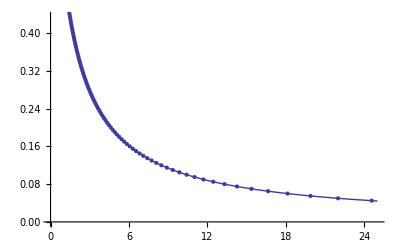

```mathematica
Show[Plot[zNum[x],{x,0,xDimMax},AxesOrigin->{0,0}],ListPlot[zNumTable,PlotRange->All]]
```

#### Energy loss is then, as before (with all the dimensions, no λ):

```mathematica
dEdxNum[x_]=1/(2π)1/(zH^2*zNum[x/zH]^2)(√fGB[0])/a/.zH->(a/(π T))/.λGB->λGBNum//Simplify
```

(1.14588 T^2)/(InterpolatingFunction[{{0.,27.776}},<>][2.90339 T x])^2

#### Compare to the analytical one:

```mathematica
dEdxAnal[xDim_]=dEdxSol[xDim/(π*T),5,λGBNum]/.λ->1/.z0->1
```

0.181258 T^2 (2.51433+2. xDim)^2

#### Note to myself: we have to compare by diving by πT, although zH in GB is not 1/(πT) - because “x” in both dEdxAnal and dEdxNum is in fm, so to put them on the same plot, we need to divide them by the same number, πT

```mathematica
dEdxNumCompare[xDim_]=dEdxNum[xDim/(π*T)];
```

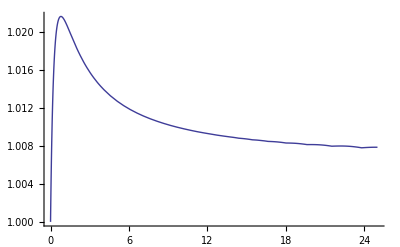

```mathematica
Plot[{Evaluate[dEdxNumCompare[xDim]/T^2]/Evaluate[dEdxAnal[xDim]/T^2]},{xDim,0,xDimMax},AxesOrigin->{0,0},PlotRange->All]
```

### GB energy loss - usable form and plots

#### 8th order of expansion is more than enough, in GeV and fm:

```mathematica
dEdxGB[x_,T_]=1/hc*Evaluate[dEdxSol[x,8,λGB]/.x->(x/hc)];
```

#### Check the CFT limit

```mathematica
ShouldBeZero=Simplify[dEdxCFT[x,T]-Limit[dEdxGB[x,T],λGB->0]]
```

0.

#### Compare to the CFT limit for various λGB

```mathematica
dEdxGBPlot=Plot[{(dEdxGB[y/(π T),T]/.λGB->(-1/36))/dEdxCFT[y/(π T),T]/.z0->1,(dEdxGB[y/(π T),T]/.λGB->(-4/36))/dEdxCFT[y/(π T),T]/.z0->1,(dEdxGB[y/(π T),T]/.λGB->(-7/36))/dEdxCFT[y/(π T),T]/.z0->1},{y,0,2},
PlotStyle->{{Thickness[0.005],ColorData[1,1]},{Thickness[0.005],ColorData[1,2]},{Thickness[0.005],ColorData[1,3]}},
PlotRange->{{0,2},{0,1}},AxesOrigin->{0,0},ImageSize->600,AspectRatio->.7,Axes->False,Frame->True,LabelStyle->{Directive[Black,12],FontFamily->"Helvetica"},RotateLabel->False, FrameLabel->{Style["πTx",FontSize->15,Italic,Bold],Style["(dE_GB/dx)/(dE/dx)",FontSize->15,Italic,Bold]}];
```

```mathematica
LabelsdEdxGBPlot=
{Graphics[Text[Style["λ_GB = -1/36",14,Italic,Bold,Black,FontFamily->"Helvetica"],{1.0,0.84},{-1,0}]],
Graphics[Text[Style["λ_GB = -4/36",14,Italic,Bold,Black,FontFamily->"Helvetica"],{1.3,0.6},{-1,0}]],
Graphics[Text[Style["λ_GB = -7/36",14,Italic,Bold,Black,FontFamily->"Helvetica"],{1.6,0.45},{-1,0}]]
};
```

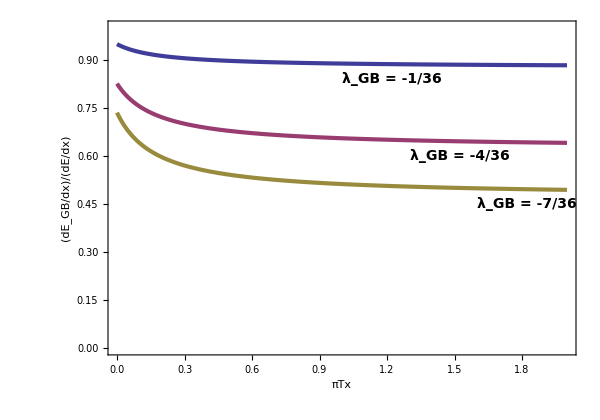

```mathematica
dEdxGBPlotForExport=Show[dEdxGBPlot,LabelsdEdxGBPlot]
```

```mathematica
(*Export["MathFigure-dEdxGBvsCFT.pdf",dEdxGBPlotForExport];*)
```

## Glauber model

### Parameters

```mathematica
bb=3; (* impact parameter in fm *)
ti=1;(* initial time in fm *)
νa=0.1; (* transverse velocity asymmetry factor, from MG's nucl-th/0109063 it is between 0.05 and 0.1 *)
```

### Constants and definitions

#### Common constants

```mathematica
hc=0.197; (* hbar*c in GeV*fm *)
χ=0.54;(* 'Diffuseness' parameter for Woods-Saxon in fm *)
nf=3; (* number of active flavors in the medium *)
FFLHC=0.6; (* effective factor to implement fragmentation functions *)
FFRHIC=0.7;
```

#### RHIC Au-Au @ √s= 200 AGeV

```mathematica
Arhic=197; (* gold *)
Rrhic=1.1*(Arhic)^(1/3);(* Gold nucleus radius in fm *)
σrhic=42 *0.1 ;(* n-n inelastic cross section in fm^2 at √s= 200 GeV per nucleon pair [1mb=0.1fm^2] *)
dNdyrhicb0=700*3/2*1.1; (* multiplicity at mid-rapidity for all particles: 700 is the dN/dη multiplicity, 3/2 to get total multiplicity from the charged one and 1.1 to convert from dN/dη to dN/dy *)
Nbinrhicb0=1222.303; (* number of binary collisions at b=0 *)
Npartrhicb0=378.462; (* number of participants at b=0 *)
```

#### LHC Pb-Pb @ √s= 2.76 ATeV

```mathematica
Alhc=207; (* lead *)
Rlhc=1.1*(Alhc)^(1/3);(* lead nucleus radius in fm *)
σlhc=63 *0.1 ;(* n-n inelastic cross section in fm^2 - from Xin-Nian's 1008.1841 *)
dNdylhcb0=1584*3/2*1.1; (* from Alice status report *)
Nbinlhcb0=1966.734;(* number of binary collisions at b=0 *)
Npartlhcb0=404.134; (* number of participants at b=0 *)
```

### Glauber model

#### Woods Saxon nuclear density profile for RHIC and LHC

```mathematica
ρ0rhic=Arhic/NIntegrate[1/(1+Exp[(r-Rrhic)/χ])*4π*r^2,{r,0,4*Rrhic}];
WSrhic[r_,z_]:=ρ0rhic/(1+Exp[(√(r^2+z^2)-Rrhic)/χ]);
ρ0lhc=Alhc/NIntegrate[1/(1+Exp[(r-Rlhc)/χ])*4π*r^2,{r,0,4*Rlhc}];
WSlhc[r_,z_]:=ρ0lhc/(1+Exp[(√(r^2+z^2)-Rlhc)/χ]);
```

#### Define and numerically evaluate the nuclear thickness function TAA for gold and lead

The “if” statement is to ensure we don’t go into extrapolation

```mathematica
TArhicRadList=Table[{r,NIntegrate[WSrhic[r,z],{z,-2Rrhic,2Rrhic}]},{r,0,2Rrhic,0.01}];
TAlhcRadList=Table[{r,NIntegrate[WSlhc[r,z],{z,-2Rlhc,2Rlhc}]},{r,0,2Rlhc,0.01}];
TArhicRadInt=Interpolation[TArhicRadList];
TAlhcRadInt=Interpolation[TAlhcRadList];
```

```mathematica
TArhicRadIntOpt[r_]:=If[r≤2Rrhic-0.01,TArhicRadInt[r],0];
TAlhcRadIntOpt[r_]:=If[r≤2Rlhc-0.01,TAlhcRadInt[r],0];
TArhic[x_,y_]:=TArhicRadIntOpt[√(x^2+y^2)];
TAlhc[x_,y_]:=TAlhcRadIntOpt[√(x^2+y^2)];
```

#### Define the number density of binary collisions TAA and the participant nucleon profile density ρpart

```mathematica
TAArhic[x_,y_]:=σrhic*TArhic[x+bb/2,y]*TArhic[x-bb/2,y]; 
ρpartrhic[x_,y_]:=TArhic[x+bb/2,y](1-Exp[-σrhic*TArhic[x-bb/2,y]])+TArhic[x-bb/2,y](1-Exp[-σrhic*TArhic[x+bb/2,y]]);
TAAlhc[x_,y_]:=σlhc*TAlhc[x+bb/2,y]*TAlhc[x-bb/2,y]; 
ρpartlhc[x_,y_]:=TAlhc[x+bb/2,y](1-Exp[-σlhc*TAlhc[x-bb/2,y]])+TAlhc[x-bb/2,y](1-Exp[-σlhc*TAlhc[x+bb/2,y]]);
```

#### Total number of participants and binary collisions

```mathematica
Nbinrhic=NIntegrate[TAArhic[x,y],{x,-2Rrhic,2Rrhic},{y,-2Rrhic,2Rrhic}] ;
Npartrhic=NIntegrate[ρpartrhic[x,y],{x,-2Rrhic,2Rrhic},{y,-2Rrhic,2Rrhic}];
Nbinlhc=NIntegrate[TAAlhc[x,y],{x,-2Rlhc,2Rlhc},{y,-2Rlhc,2Rlhc}] ;
Npartlhc=NIntegrate[ρpartlhc[x,y],{x,-2Rlhc,2Rlhc},{y,-2Rlhc,2Rlhc}];
```

#### dN/dy mixed scaling at the selected impact parameter

```mathematica
dNdyrhic=dNdyrhicb0*(0.85Npartrhic+0.15Nbinrhic)/(0.85Npartrhicb0+0.15Nbinrhicb0);
dNdylhc=dNdylhcb0*(0.85Npartlhc+0.15Nbinlhc)/(0.85Npartlhcb0+0.15Nbinlhcb0);
```

#### Stefan-Boltzmann temperature in GeV

The evolution starts at t=0, not t=ti

```mathematica
temprhic[x_,y_,t_,ϕ_]:=(π^2/1.202*1/(16+9*nf)*dNdyrhic/Npartrhic*ρpartrhic[x+t Cos[ϕ],y+t Sin[ϕ]]*1/(t+ti))^(1/3)*hc; 
templhc[x_,y_,t_,ϕ_]:=(π^2/1.202*1/(16+9*nf)*dNdylhc/Npartlhc*ρpartlhc[x+t Cos[ϕ],y+t Sin[ϕ]]*1/(t+ti))^(1/3)*hc;
```

#### Include transverse expansion from MG’s nucl-th/0109063, two types of blast wave

```mathematica
vrhic=0.6;vlhc=0.6;
rBlast1rhic[t_]:=1+(vrhic*t)/Rrhic;
rBlast1lhc[t_]:=1+(vlhc*t)/Rlhc;
rBlast2rhic[t_]:=√(1+((vrhic*t)/Rrhic)^2);
rBlast2lhc[t_]:=√(1+((vlhc*t)/Rlhc)^2);
```

```mathematica
temprhicTrExp1[x_,y_,t_,ϕ_]:=(π^2/1.202*1/(16+9*nf)*dNdyrhic/Npartrhic*ρpartrhic[(x+t Cos[ϕ])/rBlast1rhic[t],(y+t Sin[ϕ])/rBlast1rhic[t]]*1/(t+ti)*1/rBlast1rhic[t]^2)^(1/3)*hc; 
templhcTrExp1[x_,y_,t_,ϕ_]:=(π^2/1.202*1/(16+9*nf)*dNdylhc/Npartlhc*ρpartlhc[(x+t Cos[ϕ])/rBlast1lhc[t],(y+t Sin[ϕ])/rBlast1lhc[t]]*1/(t+ti)*1/rBlast1lhc[t]^2)^(1/3)*hc;
```

```mathematica
temprhicTrExp2[x_,y_,t_,ϕ_]:=(π^2/1.202*1/(16+9*nf)*dNdyrhic/Npartrhic*ρpartrhic[(x+t Cos[ϕ])/rBlast2rhic[t],(y+t Sin[ϕ])/rBlast2rhic[t]]*1/(t+ti)*1/rBlast2rhic[t]^2)^(1/3)*hc; 
templhcTrExp2[x_,y_,t_,ϕ_]:=(π^2/1.202*1/(16+9*nf)*dNdylhc/Npartlhc*ρpartlhc[(x+t Cos[ϕ])/rBlast2lhc[t],(y+t Sin[ϕ])/rBlast2lhc[t]]*1/(t+ti)*1/rBlast2lhc[t]^2)^(1/3)*hc;
```

#### Asymmetric transverse expansion from MG’s nucl-th/0109063

```mathematica
RxRhic=Rrhic-bb/2;RyRhic=√(Rrhic^2-bb^2/4);
RxLhc=Rlhc-bb/2;RyLhc=√(Rlhc^2-bb^2/4);
```

```mathematica
vT=0.6;vx=vT*(1+νa);vy=vT*(1-νa);
```

```mathematica
rBlRhicX[t_]:=√(1+((vx*t)/RxRhic)^2);rBlRhicY[t_]:=√(1+((vy*t)/RyRhic)^2)
rBlLhcX[t_]:=√(1+((vx*t)/RxLhc)^2);rBlLhcY[t_]:=√(1+((vy*t)/RyLhc)^2)
```

```mathematica
temprhicTrExpAs[x_,y_,t_,ϕ_]:=(π^2/1.202*1/(16+9*nf)*dNdyrhic/Npartrhic*ρpartrhic[(x+t Cos[ϕ])/rBlRhicX[t],(y+t Sin[ϕ])/rBlRhicY[t]]*1/(t+ti)*1/(rBlRhicX[t]*rBlRhicY[t]))^(1/3)*hc; 
templhcTrExpAs[x_,y_,t_,ϕ_]:=(π^2/1.202*1/(16+9*nf)*dNdylhc/Npartlhc*ρpartlhc[(x+t Cos[ϕ])/rBlLhcX[t],(y+t Sin[ϕ])/rBlLhcY[t]]*1/(t+ti)*1/(rBlLhcX[t]*rBlLhcY[t]))^(1/3)*hc;
```

#### Initial temperature profile

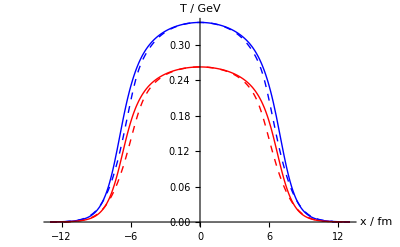

```mathematica
Plot[{templhc[x,0,0,0],temprhic[x,0,0,0],templhc[0,x,0,0],temprhic[0,x,0,0]},{x,-2Rlhc,2Rlhc},PlotStyle->{{Blue,Dashed},{Red,Dashed},{Blue},{Red}},AxesLabel->{"x / fm","T / GeV"}]
```

### Production spectra

#### dσ/dpT for light quarks at RHIC and LHC, taken from ‘Wicks-gucb-RHIC-LHC.nb’ (x is in GeV)

```mathematica
lightdσdpti200[x_] :=Exp[4.21108+492.3337185819615 Log[x]^0.33-1563.9730328289304 Log[x]^0.5+1366.88550980224 Log[x]^0.66+15.328171861165465 Log[x]^2-1.1738997665593238 Log[x]^3]/x^314.171323374679
```

```mathematica
lightdσdpti5500[x_] :=Exp[6.542622376702832+124.45345845004297 Log[x]^0.33-366.0172645088978 Log[x]^0.5+294.6590734461218 Log[x]^0.66+1.499811062159335 Log[x]^2-0.07678983744859756 Log[x]^3]/x^59.09821038058;
```

## Data

### CMS v2 data

```mathematica
Needs["PlotLegends`"];
```

#### This is the CMS v2 data for centralities 20-30%, digitized from Fig. 1 of 1204.1850

```mathematica
(*-Graphics-*)
```

```mathematica
cmsv2={{1.006993,0.11594594},{1.1328671,0.12621622},{1.2587413,0.1354054},{1.4265734,0.14972973},{1.5944057,0.16243243},{1.8881118,0.17621621},{2.013986,0.1845946},{2.3076923,0.19351351},{2.6013987,0.20405406},{3.6503496,0.20594594},{4.3636365,0.18378378},{5.034965,0.15648648},{5.874126,0.12891892},{6.713287,0.113513514},{8.055944,0.098378375},{10.531468,0.06837838},{12.797203,0.0627027},{14.811189,0.06297297},{17.286713,0.05945946},{21.104895,0.04810811},{26.013987,0.045135137},{31.51049,0.03054054},{39.9021,0.018648649},{53.244755,0.03891892}};
```

#### Plot

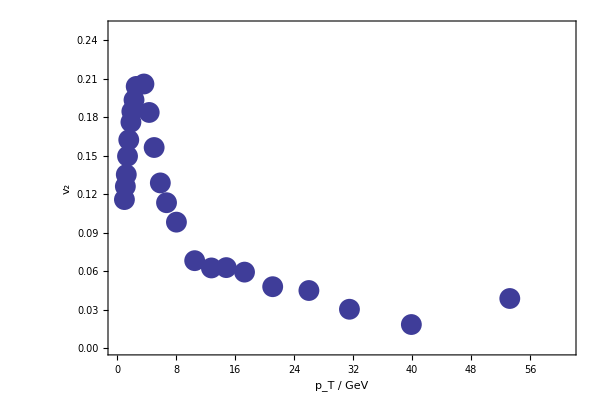

```mathematica
CMSv2Plot=ListPlot[cmsv2,PlotStyle->{{PointSize[0.025],ColorData[1,1]}},PlotRange->{{0,61},{0,0.25}},Joined->{False},ImageSize->600,Axes->False,AspectRatio->.7,Frame->True,RotateLabel->True,AxesOrigin->{0,0},LabelStyle->{Directive[Black,12],FontFamily->"Helvetica"},FrameLabel->{Style["p_T / GeV",FontSize->15,Italic,Bold],Style["v_2",FontSize->15,Italic,Bold]},RotateLabel->False]
```

### LHC central collisions

#### Data from CMS, 2012 PbPb @ 2.76 TeV RAA data for 0 - 5 % centrality (taken from Figure 5 of 1202.2554)

```mathematica
(*-Graphics-*)
```

```mathematica
CMSraafg5f={{1.05645,0.34,0.365166,0.39},{1.16988,0.35,0.382461,0.4},{1.2955,0.37,0.393234,0.425},{1.50374,0.387,0.412658,0.44},{1.69153,0.39,0.423417,0.456},{1.90277,0.39,0.423306,0.456},{2.09061,0.385,0.423217,0.45},{2.31508,0.38,0.414425,0.445},{2.79471,0.345,0.366421,0.392},{3.56418,0.25,0.268365,0.3},{4.33649,0.175,0.196441,0.215},{5.15342,0.14,0.157148,0.175},{5.98179,0.127,0.143963,0.165},{6.72882,0.129,0.1482,0.166},{8.38183,0.142,0.161036,0.176},{10.6896,0.172,0.191241,0.205},{13.2116,0.205,0.230172,0.25},{16.8491,0.265,0.282116,0.31},{21.6573,0.34,0.37101,0.4},{26.1443,0.37,0.405614,0.446},{32.0599,0.39,0.444552,0.497},{38.3996,0.45,0.529165,0.605},{44.5721,0.44,0.518154,0.605},{54.2303,0.47,0.53536,0.59},{67.0247,0.56,0.641682,0.718},{80.2786,0.47,0.53499,0.6},{95.4019,0.43,0.523957,0.613}};
```

#### Extract error bands

```mathematica
CMSfg5fm=Table[{CMSraafg5f[[i,1]],CMSraafg5f[[i,3]]},{i,1,Length[CMSraafg5f]}];
CMSfg5fl=Table[{CMSraafg5f[[i,1]],CMSraafg5f[[i,2]]},{i,1,Length[CMSraafg5f]}];
CMSfg5fh=Table[{CMSraafg5f[[i,1]],CMSraafg5f[[i,4]]},{i,1,Length[CMSraafg5f]}];
```

#### Plot

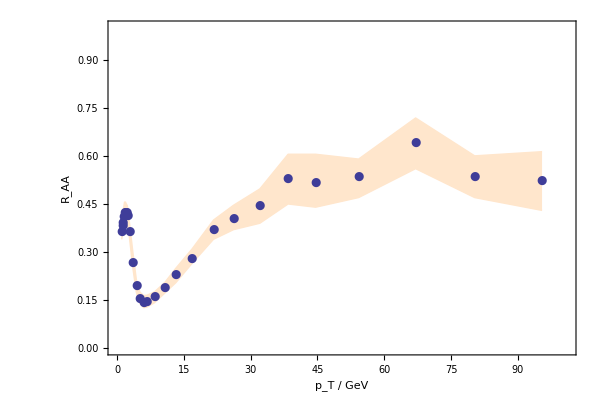

```mathematica
CMSPlot=ListPlot[
{CMSfg5fm,CMSfg5fl,CMSfg5fh},
PlotStyle->{{PointSize[0.012],ColorData[1,1]},{LightOrange},{LightOrange}},
PlotMarkers->{Style["●",12],"",""},Filling->{{2->{{3},Directive[LightOrange,Thickness[0.00]]}}},
Joined->{False,True,True},
PlotRange->{{0,101},{0,1}},ImageSize->600,Axes->False,AspectRatio->.7,Frame->True,AxesOrigin->{0,0},RotateLabel->True,
LabelStyle->{Directive[Black,12],FontFamily->"Helvetica"},
FrameLabel->{Style["p_T / GeV",FontSize->15,Italic,Bold],Style["R_AA",FontSize->15,Italic,Bold]}]
```

### PHENIX central collisions

#### PHENIX data on RAA of π^0, 0-5% centrality, Au+Au, √s_NN=200 GeV (from 1208.2254, Fig. 13, digitized)

```mathematica
(*-Graphics-*)
```

```mathematica
phenixRAAc={{5.2473288,0.17710344},{5.7475266,0.17627586},{6.241393,0.17627586},{6.741591,0.18372414},{7.241789,0.17462069},{7.7419868,0.1804138},{8.242185,0.19034483},{8.7487135,0.17627586},{9.248912,0.20855172},{9.755442,0.23006897},{10.996438,0.20772414},{13.009893,0.2457931},{15.010685,0.2995862},{16.998814,0.31448275},{19.012268,0.33103448}};
```

```mathematica
phenixRAAu={{5.2473288,0.19862069},{5.7538586,0.19944827},{6.2477245,0.20027587},{6.741591,0.20772414},{7.2481203,0.19862069},{7.7419868,0.20606896},{8.242185,0.21517241},{8.7487135,0.20027587},{9.248912,0.23586208},{9.749109,0.25903448},{11.00277,0.23917241},{12.99723,0.29875863},{15.004353,0.38317242},{16.998814,0.4262069},{19.012268,0.47668967}};
```

```mathematica
phenixRAAd={{5.2409973,0.15144828},{5.741195,0.15144828},{6.2477245,0.15227586},{6.735259,0.15889655},{7.241789,0.15144828},{7.7546496,0.15806897},{8.242185,0.16717242},{8.736051,0.15558621},{9.255243,0.18289655},{9.742778,0.20027587},{10.996438,0.17710344},{13.003562,0.19365518},{15.010685,0.216},{17.005144,0.2035862},{19.012268,0.18786207}};
```

#### Plot of only the Phenix data

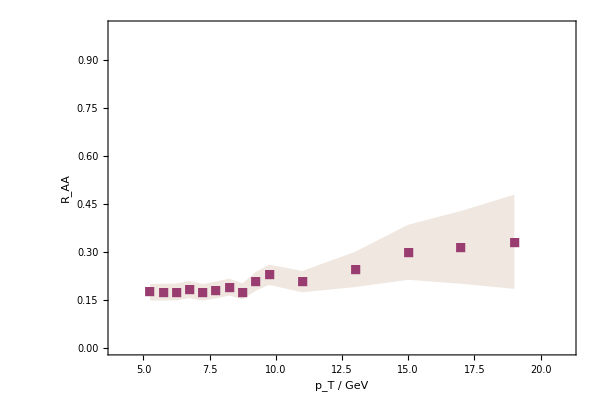

```mathematica
PHENIXPlot=ListPlot[
{phenixRAAc,phenixRAAd,phenixRAAu},
PlotStyle->{{PointSize[0.012],ColorData[1,2]},{LightBrown},{LightBrown}},
PlotMarkers->{Style["■",12],"",""},Filling->{{2->{{3},Directive[LightBrown,Thickness[0.00]]}}},
Joined->{False,True,True},
PlotRange->{{4,21},{0,1}},ImageSize->600,Axes->False,AspectRatio->.7,Frame->True,AxesOrigin->{0,0},RotateLabel->True,
LabelStyle->{Directive[Black,12],FontFamily->"Helvetica"},
FrameLabel->{Style["p_T / GeV",FontSize->15,Italic,Bold],Style["R_AA",FontSize->15,Italic,Bold]}]
```

#### Plot of the Phenix data together with the CMS

```mathematica
JoinedCMSPHENIX=ListPlot[
{CMSfg5fm,phenixRAAc,phenixRAAd,phenixRAAu,CMSfg5fl,CMSfg5fh},
PlotStyle->{{PointSize[0.012],ColorData[1,1]},{PointSize[0.012],ColorData[1,2]},{LightBrown},{LightBrown},{LightOrange},{LightOrange}},
PlotMarkers->{Style["●",12],Style["■",12],"","","",""},Filling->{{3->{{4},Directive[LightBrown,Thickness[0.00]]}},{5->{{6},Directive[LightOrange,Thickness[0.00]]}}},
Joined->{False,False,True,True,True,True},
PlotRange->{{0,101},{0,1}},ImageSize->600,Axes->False,AspectRatio->.7,Frame->True,AxesOrigin->{0,0},RotateLabel->True,
LabelStyle->{Directive[Black,12],FontFamily->"Helvetica"},
FrameLabel->{Style["p_T / GeV",FontSize->15,Italic,Bold],Style["R_AA",FontSize->15,Italic,Bold]}];
```

### PHENIX RAA in&out data

#### Data for 20-30% centrality at PHENIX, obtained by digitizing Figure 22 in 1208.2254

```mathematica
(*-Graphics-*)
```

```mathematica
RAAOutPhenixCenterList={{5.2468953,0.26496017},{6.2534695,0.2784479},{7.2410517,0.26993975},{8.257122,0.30656525},{9.263696,0.29812166},{10.754565,0.33752185},{12.767714,0.38212922},{14.752374,0.5005655},{16.765522,0.3797649}};
RAAOutPhenixUpperList={{5.2658877,0.27416083},{6.2534695,0.2872242},{7.250548,0.2784479},{8.266618,0.32017753},{9.263696,0.3172106},{10.754565,0.36588308},{12.758218,0.428623},{14.742878,0.60864854},{16.765522,0.5342725}};
RAAOutPhenixLowerList={{5.2563915,0.25846332},{6.2534695,0.26993975},{7.231556,0.25926664},{8.257122,0.2926222},{9.263696,0.2784479},{10.754565,0.31524795},{12.748722,0.3354335},{14.752374,0.39539853},{16.765522,0.23258239}};
```

```mathematica
RAAInPhenixCenterList={{5.493791,0.43263197},{6.5003653,0.41681764},{7.516435,0.40282953},{8.504018,0.40408152},{9.501096,0.41167572},{11.001461,0.42202377},{13.005114,0.42202377},{14.9992695,0.59005094},{17.002922,0.60114014}};
RAAInPhenixUpperList={{5.493791,0.44626793},{6.509861,0.42995518},{7.516435,0.41552618},{8.513514,0.42333546},{9.501096,0.4366784},{11.010957,0.45044193},{13.005114,0.47484282},{15.008765,0.7086052},{17.012419,0.81227577}};
RAAInPhenixLowerList={{5.503287,0.42202377},{6.5003653,0.40659723},{7.516435,0.39173457},{8.504018,0.3881046},{9.501096,0.3881046},{11.010957,0.3941734},{12.995617,0.3716044},{14.9992695,0.47631863},{17.002922,0.39786017}};
```

#### For plots of in, out and central, we need to separate the points from the bands

```mathematica
PHENIXPlotIn=ListPlot[{RAAInPhenixLowerList,RAAInPhenixUpperList},PlotStyle->{{LightPink},{LightPink}},Joined->{True,True},Filling->{{1->{{2},Directive[LightPink]}}},PlotRange->{{4,21},{0,1}},ImageSize->600,Axes->False,AspectRatio->.7,Frame->True,AxesOrigin->{0,0},RotateLabel->True,
LabelStyle->{Directive[Black,12],FontFamily->"Helvetica"},
FrameLabel->{Style["p_T / GeV",FontSize->15,Italic,Bold],Style["R_AA",FontSize->15,Italic,Bold]}];
```

```mathematica
PHENIXPlotOut=ListPlot[{RAAOutPhenixLowerList,RAAOutPhenixUpperList},PlotStyle->{{LightYellow},{LightYellow}},Joined->{True,True},Filling->{{1->{{2},Directive[LightYellow]}}},PlotRange->{{4,21},{0,1}},ImageSize->600,Axes->False,AspectRatio->.7,Frame->True,AxesOrigin->{0,0},RotateLabel->True,
LabelStyle->{Directive[Black,12],FontFamily->"Helvetica"},
FrameLabel->{Style["p_T / GeV",FontSize->15,Italic,Bold],Style["R_AA",FontSize->15,Italic,Bold]}];
```

```mathematica
PHENIXPlotsCentral=ListPlot[{phenixRAAd,phenixRAAu},PlotStyle->{{LightBrown},{LightBrown}},Joined->{True,True},Filling->{{1->{{2},Directive[LightBrown]}}},PlotRange->{{4,21},{0,1}},ImageSize->600,Axes->False,AspectRatio->.7,Frame->True,AxesOrigin->{0,0},RotateLabel->True,
LabelStyle->{Directive[Black,12],FontFamily->"Helvetica"},
FrameLabel->{Style["p_T / GeV",FontSize->15,Italic,Bold],Style["R_AA",FontSize->15,Italic,Bold]}];
```

```mathematica
PHENIXPlotsPoints=ListPlot[
{RAAInPhenixCenterList,RAAOutPhenixCenterList,phenixRAAc},
PlotStyle->{
{PointSize[0.15],ColorData[1,4]},{PointSize[0.15],ColorData[1,5]},{PointSize[0.15],ColorData[1,2]}},
PlotMarkers->{Style["▲",14],Style["▼",14],Style["■",12]},
Joined->{False,False,False},
PlotRange->{{4,21},{0,1}},ImageSize->600,Axes->False,AspectRatio->.7,Frame->True,AxesOrigin->{0,0},RotateLabel->True,
LabelStyle->{Directive[Black,12],FontFamily->"Helvetica"},
FrameLabel->{Style["p_T / GeV",FontSize->15,Italic,Bold],Style["R_AA",FontSize->15,Italic,Bold]}];
```

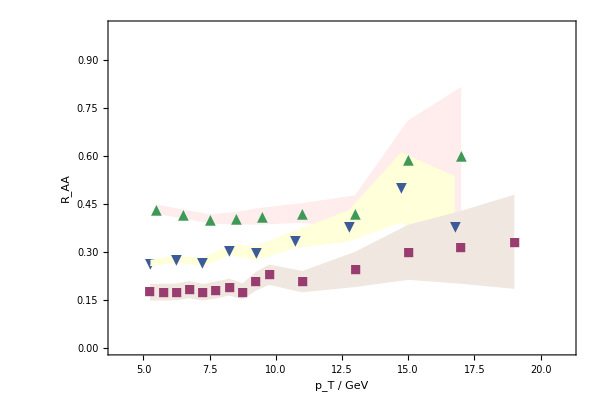

```mathematica
PHENIXAllPlots=Show[PHENIXPlotIn,PHENIXPlotOut,PHENIXPlotsCentral,PHENIXPlotsPoints]
```

## Computation of R_AA

### Parameters

```mathematica
λ=4;(* 't Hooft coupling *)
Angle="in"; (* can be "in" -> ϕ=0 or "out" -> ϕ=π/2 *)
Acc="LHC"; (* can be "LHC" or "RHIC" *)
EnLoss="CFT-GB-corrected"; (* can be "CFT", "CFT-corrected" or "CFT-GB-corrected" *)
z0=1; (* Initial dimensionless z *)
TrExp="TrMod"; (* can be "none", "TrLin" or "TrMod" or "TrModAs" *)
κTemp=0.9; (* Temperature factor *)
λGB=-0.2; (* in case GB corrections will be used *)
Tfreeze=0.17; (* freeze-out temperature in GeV *)
```

### Preset of the code

#### Define the temperature, energy loss and spectra to be used depending on the case of lhc or rhic

EfSet is the set of final energies at which the RAA will be computed

```mathematica
If[Acc=="LHC",{
If[TrExp=="none",temp[x0_,y0_,t_,ϕ_]:=κTemp*templhc[x0,y0,t,ϕ];];
If[TrExp=="TrLin",temp[x0_,y0_,t_,ϕ_]:=κTemp*templhcTrExp1[x0,y0,t,ϕ];];
If[TrExp=="TrMod",temp[x0_,y0_,t_,ϕ_]:=κTemp*templhcTrExp2[x0,y0,t,ϕ];];
If[TrExp=="TrModAs",temp[x0_,y0_,t_,ϕ_]:=κTemp*templhcTrExpAs[x0,y0,t,ϕ];];
dσdpti[x_]:=lightdσdpti5500[x];
R0=Rlhc;
Nbin=Nbinlhc;
TAA[x_,y_]:=TAAlhc[x,y];
EfSet={10,20,30,40,50,60,70,80,90,100,110,120,130,140,150,160,170};
}];
```

```mathematica
If[Acc=="RHIC",{
If[TrExp=="none",temp[x0_,y0_,t_,ϕ_]:=κTemp*temprhic[x0,y0,t,ϕ];];
If[TrExp=="TrLin",temp[x0_,y0_,t_,ϕ_]:=κTemp*temprhicTrExp1[x0,y0,t,ϕ];];
If[TrExp=="TrMod",temp[x0_,y0_,t_,ϕ_]:=κTemp*temprhicTrExp2[x0,y0,t,ϕ];];
If[TrExp=="TrModAs",temp[x0_,y0_,t_,ϕ_]:=κTemp*temprhicTrExpAs[x0,y0,t,ϕ];];
dσdpti[x_]:=lightdσdpti200[x];
R0=Rrhic;
Nbin=Nbinrhic;
TAA[x_,y_]:=TAArhic[x,y];
EfSet={5,10,20,30,40,50,60};
}];
```

#### Determine the energy loss to use

tempInt[t] is the temperature to be interpolated to speed up the computation

```mathematica
If[EnLoss=="CFT",dEdx[t_]:=dEdxCFT[t,tempInt[t]];];
If[EnLoss=="CFT-corrected",dEdx[t_]:=dEdxCFT[t,tempInt[t]*3^(-1/4)];];
If[EnLoss=="CFT-GB-corrected",dEdx[t_]:=dEdxGB[t,tempInt[t]*3^(-1/4)];];
```

#### Depending on whether you chose RAA in or out, determine the limits of integration

Because ϕ=0 is the x-direction, then one has to go in x from -2R to +2R, while it is symmetric around y=0, so we need to go from y=0 to y=2R

```mathematica
If[Angle=="in",ϕ=0];
If[Angle=="out",ϕ=π/2];
If[ϕ==0,{xStart=-2R0;yStart=0;},{xStart=0;yStart=-2R0;}];
```

#### Set the step in x-y plane in fm and see through how many steps the main loop will have to go (for time estimate)

The default option used to be 0.8, but since the code is now fast, this can be more fine, but the results remain practically unchanged

```mathematica
xystep=0.8;
NSteps=0;
Do[If[temp[x0,y0,0,0]>Tfreeze,NSteps=NSteps+1;];,{x0,xStart,2R0,xystep},{y0,yStart,2R0,xystep}];
NSteps
```

107

#### Save the parameters (these will be saved in the external file)

```mathematica
If[TrExp=="none",TrExpSave="TrExp = 0";];
If[TrExp=="TrLin",TrExpSave="TrExp = Lin";];
If[TrExp=="TrMod",TrExpSave="TrExp = Sqrt";];
If[TrExp=="TrModAs",TrExpSave="TrExp = SqrtAs, νa = "<>ToString[νa];];
```

```mathematica
If[EnLoss=="CFT",EnLossSave="CFT";];
If[EnLoss=="CFT-corrected",EnLossSave="CFT-Corr";];
If[EnLoss=="CFT-GB-corrected",EnLossSave="CFT-GB-Corr, λGB = "<>ToString[λGB];];
```

```mathematica
Params={Acc,"b = "<>ToString[bb],"ti = "<>ToString[ti], TrExpSave,"Tfreeze = "<>ToString[Tfreeze],"KappaTemp = "<>ToString[κTemp],"Phi = "<>ToString[Angle],"Lambda = "<>ToString[N[λ]],EnLossSave,"z0 = "<>ToString[z0]}
```

{LHC,b = 3,ti = 1,TrExp = Sqrt,Tfreeze = 0.17,KappaTemp = 0.9,Phi = in,Lambda = 4.,CFT-GB-Corr, λGB = -0.2,z0 = 1}

### Main code

#### Main loop that computes RAA for each (x0,y0)

The temperature and dE/dx are first interpolated over the path, and then numerically integrated, as that speeds up the whole process drastically.

```mathematica
count=0;
ProgressIndicator[Dynamic[count],{0,NSteps}]
Do[RAA[EfSet[[i]]]={};,{i,1,Length[EfSet]}];
Do[
If[Re[temp[x0,y0,0,ϕ]]>Tfreeze,
{
tf=t/.FindRoot[Re[temp[x0,y0,t,ϕ]]==Tfreeze,{t,R0,0,4R0}];
tempInt=Quiet[Interpolation[Table[{t,temp[x0,y0,t,ϕ]},{t,0,tf+0.02,0.01}]]];
dEdxInt2=Quiet[Interpolation[Table[{t,dEdx[t]},{t,0,tf+0.02,0.01}]]];
ΔE=NIntegrate[dEdxInt2[t],{t,0,tf}];
Do[RAALocal=dσdpti[Ef+ΔE]/dσdpti[Ef];RAA[Ef]=Append[RAA[Ef],{x0,y0,RAALocal}];,{Ef,EfSet}];
count=count+1;
},
{
Do[RAALocal=0;RAA[Ef]=Append[RAA[Ef],{x0,y0,RAALocal}];,{Ef,EfSet}];
}];
,{x0,xStart,2R0,xystep}
,{y0,yStart,2R0,xystep}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

#### Find averaged RAA for each Ef

```mathematica
RAAList={};
Do[
RAAInt=Interpolation[RAA[Ef]];
IntInt=Quiet[Interpolation[Flatten[Table[{{x,y},TAA[x,y]*RAAInt[x,y]},{x,xStart,2R0,xystep},{y,yStart,2R0,xystep}],1]]];
RAAAv=2/Nbin*Quiet[NIntegrate[IntInt[x,y],{x,xStart,2R0},{y,yStart,2R0}]];
RAAList=Append[RAAList,{Ef,RAAAv}];
,{Ef,EfSet}];
```

### Append the results to an external file

```mathematica
fSave=OpenAppend["RAAResults.dat"];
Write[fSave,Params];
Write[fSave,RAAList];
Close[fSave];
```

## Load the R_AA results and plot

### Load the RAA results and interpolate

#### Load the RAA results and interpolate

```mathematica
RAAInput=ReadList["RAAResults.dat"];
nMax=Length[RAAInput]/2;
Do[
ParamsCase[i]=RAAInput[[2i-1]];
RAACase[i]=RAAInput[[2i]];
RAACaseInt[i]=Interpolation[RAACase[i]];
If[ParamsCase[i][[1]]=="LHC",{RAAOpt[i][x_]=If[x>10&&x<170,Evaluate[RAACaseInt[i][x]]];}];
If[ParamsCase[i][[1]]=="RHIC",{RAAOpt[i][x_]=If[x>5&&x<60,Evaluate[RAACaseInt[i][x]]];}];
,{i,1,nMax,1}];
```

#### Prepare the parameter table for display

```mathematica
ParamsDisplay={{Style["n",Bold],Style["Acc",Bold],Style["b",Bold],Style["t_i",Bold],Style["TrExp",Bold],Style["T_freeze",Bold],Style["κ_temp",Bold],Style["ϕ",Bold],Style["λ",Bold],Style["EnLoss",Bold],Style["z_0",Bold]}};
```

```mathematica
Do[
ParamsCaseTrimmed[i]={i,
ParamsCase[i][[1]],
StringDrop[ParamsCase[i][[2]],4],
StringDrop[ParamsCase[i][[3]],5],
StringDrop[ParamsCase[i][[4]],8],
StringDrop[ParamsCase[i][[5]],10],
StringDrop[ParamsCase[i][[6]],12],
StringDrop[ParamsCase[i][[7]],6],
StringDrop[ParamsCase[i][[8]],9],
ParamsCase[i][[9]],
StringDrop[ParamsCase[i][[10]],5]};
,{i,1,nMax}];
```

```mathematica
Do[ParamsDisplay=Append[ParamsDisplay,ParamsCaseTrimmed[i]];,{i,1,nMax}]
ParamsTable=Grid[ParamsDisplay,Dividers->{{False,True,True,False,False,False,False,False,True},{False,True}},Background->{{LightGray},{LightGray}},Spacings->{2,1}];
```

#### Trim the parameter lists for display in the plots

```mathematica
Do[
ParamsPlot[i]=
ParamsCase[i][[1]]<>" | "<>
ParamsCase[i][[2]]<>", "<>
"t_i = "<>ParamsCaseTrimmed[i][[3+1]]<>", "<>
ParamsCase[i][[4]]<>", "<>
"T_freeze = "<>ParamsCaseTrimmed[i][[5+1]]<>", "<>
"κ_temp = "<>ParamsCaseTrimmed[i][[6+1]]<>", "<>
"ϕ = "<>ParamsCaseTrimmed[i][[7+1]]<>" | "<>
"λ = "<>ParamsCaseTrimmed[i][[8+1]]<>", "<>
ParamsCase[i][[9]]<>", "<>
"z_0 = "<>ParamsCaseTrimmed[i][[10+1]];
,{i,1,nMax}]
```

### Automated plots

#### Automated central RAA plots

```mathematica
RAACentralPlots[list_]:=Show[JoinedCMSPHENIX,
Plot[Evaluate[Table[If[ParamsCase[i][[1]]=="LHC",RAAOpt[i][x/FFLHC],RAAOpt[i][x/FFRHIC]],{i,list}]],{x,0,100},PlotStyle->Thickness[0.004]],
Table[Graphics[Text[Style[ParamsPlot[list[[i]]],9,Italic,Black,FontFamily->"Helvetica"],
{10,0.96-(i-1)*0.045},{-1,0}]],{i,1,Length[list]}],
Table[Graphics[{Thickness[0.005],ColorData[1,i],
Line[{{4,0.96-(i-1)*0.045},{8,0.96-(i-1)*0.045}}]}],{i,1,Length[list]}]];
```

#### Automated off-central RHIC plots

```mathematica
RAARHICOffCentralPlots[list_]:=Show[PHENIXAllPlots,
Plot[Evaluate[Table[If[ParamsCase[i][[1]]=="LHC",RAAOpt[i][x/FFLHC],RAAOpt[i][x/FFRHIC]],{i,list}]],{x,0,100},PlotStyle->Thickness[0.004]],
Table[Graphics[Text[Style[ParamsPlot[list[[i]]],9,Italic,Black,FontFamily->"Helvetica"],
{5.6,0.96-(i-1)*0.045},{-1,0}]],{i,1,Length[list]}],
Table[Graphics[{Thickness[0.005],ColorData[1,i],
Line[{{4.5,0.96-(i-1)*0.045},{5.2,0.96-(i-1)*0.045}}]}],{i,1,Length[list]}]];
```

#### Automated LHC v2 plots

```mathematica
v2List[list_]:=Table[{RAAInput[[2*list[[1]]]][[i,1]]*FFLHC,Abs[RAAInput[[2*list[[1]]]][[i,2]]-RAAInput[[2*list[[2]]]][[i,2]]]/(RAAInput[[2*list[[1]]]][[i,2]]+RAAInput[[2*list[[2]]]][[i,2]])},{i,1,Length[RAAInput[[2*list[[1]]]]]}];
```

```mathematica
v2LHCPlots[list_]:=Show[
CMSv2Plot,
ListPlot[Table[v2List[list[[i]]],{i,1,Length[list]}],Joined->True,PlotStyle->{Thickness[0.005]}],
Table[Graphics[Text[Style[ParamsPlot[list[[i,1]]],9,Italic,Black,FontFamily->"Helvetica"],
{12,0.24-(i-1)*0.011},{-1,0}]],{i,1,Length[list]}],
Table[Graphics[{Thickness[0.006],ColorData[1,i],
Line[{{8.5,0.24-(i-1)*0.011},{10.5,0.24-(i-1)*0.011}}]}],{i,1,Length[list]}]];
```

### Select plots and compare

#### From here one chooses the available plots

```mathematica
ParamsTable
```

n | Acc | b | t_i | TrExp | T_freeze | κ_temp | ϕ | λ | EnLoss | z_0
1 | LHC | 3 | 1 | Sqrt | 0.17 | 1 | in | 1. | CFT-GB-Corr, λGB = -0.2 | 1
2 | RHIC | 3 | 1 | Sqrt | 0.17 | 1 | in | 0.25 | CFT-Corr | 1
3 | RHIC | 3 | 1 | Sqrt | 0.17 | 1 | in | 3. | CFT-Corr | 1
4 | RHIC | 3 | 1 | Sqrt | 0.17 | 1 | in | 1. | CFT-Corr | 1
5 | LHC | 3 | 1 | Sqrt | 0.17 | 1 | in | 0.25 | CFT-Corr | 1
6 | LHC | 3 | 1 | Sqrt | 0.17 | 1 | in | 3. | CFT-Corr | 1
7 | LHC | 3 | 1 | Sqrt | 0.17 | 1 | in | 1. | CFT-Corr | 1
8 | RHIC | 7 | 1 | Sqrt | 0.17 | 1 | in | 3. | CFT-Corr | 1
9 | RHIC | 7 | 1 | Sqrt | 0.17 | 1 | out | 3. | CFT-Corr | 1
10 | LHC | 7 | 1 | Sqrt | 0.17 | 1 | in | 1. | CFT-GB-Corr, λGB = -0.2 | 1
11 | LHC | 7 | 1 | Sqrt | 0.17 | 1 | out | 1. | CFT-GB-Corr, λGB = -0.2 | 1
12 | LHC | 9 | 1 | Sqrt | 0.17 | 1 | in | 1. | CFT-GB-Corr, λGB = -0.2 | 1
13 | LHC | 9 | 1 | Sqrt | 0.17 | 1 | out | 1. | CFT-GB-Corr, λGB = -0.2 | 1
14 | RHIC | 3 | 1 | Sqrt | 0.17 | 1 | in | 1. | CFT-GB-Corr, λGB = -0.2 | 1
15 | RHIC | 3 | 0.6 | Sqrt | 0.17 | 1 | in | 1. | CFT-GB-Corr, λGB = -0.2 | 1
16 | RHIC | 3 | 0.6 | Sqrt | 0.17 | 1 | in | 1. | CFT-Corr | 1
17 | RHIC | 3 | 0.6 | Sqrt | 0.17 | 1 | in | 4. | CFT-GB-Corr, λGB = -0.2 | 1
18 | LHC | 3 | 1 | Sqrt | 0.17 | 1 | in | 4. | CFT-GB-Corr, λGB = -0.2 | 1
19 | LHC | 3 | 1 | Sqrt | 0.17 | 0.9 | in | 4. | CFT-GB-Corr, λGB = -0.2 | 1
20 | LHC | 3 | 1 | Sqrt | 0.17 | 0.9 | in | 4. | CFT-GB-Corr, λGB = -0.2 | 1
21 | LHC | 7 | 1 | Sqrt | 0.17 | 0.9 | in | 4. | CFT-GB-Corr, λGB = -0.2 | 1
22 | LHC | 7 | 1 | Sqrt | 0.17 | 0.9 | out | 4. | CFT-GB-Corr, λGB = -0.2 | 1
23 | LHC | 9 | 1 | Sqrt | 0.17 | 0.9 | in | 4. | CFT-GB-Corr, λGB = -0.2 | 1
24 | LHC | 9 | 1 | Sqrt | 0.17 | 0.9 | out | 4. | CFT-GB-Corr, λGB = -0.2 | 1
25 | RHIC | 3 | 1 | Sqrt | 0.17 | 1 | in | 0.25 | CFT-Corr | 1
26 | RHIC | 3 | 1 | Sqrt | 0.17 | 1 | in | 3. | CFT-Corr | 1
27 | RHIC | 3 | 1 | Sqrt | 0.17 | 1 | in | 1. | CFT-Corr | 1
28 | LHC | 3 | 1 | Sqrt | 0.17 | 1 | in | 0.25 | CFT-Corr | 1
29 | LHC | 3 | 1 | Sqrt | 0.17 | 1 | in | 3. | CFT-Corr | 1
30 | LHC | 3 | 1 | Sqrt | 0.17 | 1 | in | 1. | CFT-Corr | 1
31 | LHC | 3 | 1 | Sqrt | 0.17 | 1 | in | 1. | CFT-Corr | 1

#### Select n of the plots to display

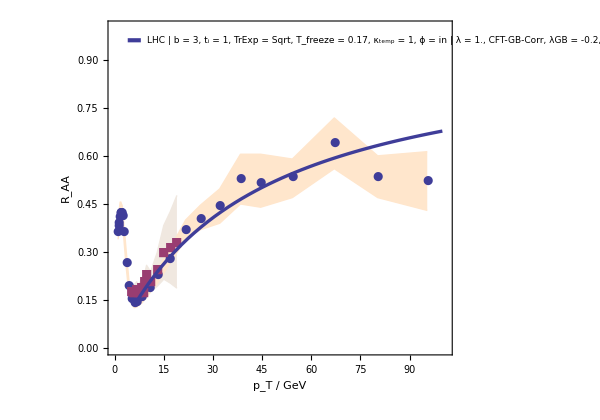

```mathematica
RAACentralPlots[{1}]
```

```mathematica
(*RAARHICOffCentralPlots[{2,3,4}]*)
```

```mathematica
(*v2LHCPlots[{{10,11},{12,13}}]*)
```

## Plots for paper

### Intro figure

#### For λGB=-0.2 and λ=0.01 old falling strings results

```mathematica
RAAFall001={{10,0.2608398010635869},{40,0.46660836068072986},{70,0.5539901911745534},{100,0.6064524105934254},{130,0.6426516388374827},{160,0.6696598205443431}};
```

#### For λGB=-0.2 and λ=1 old falling strings results

```mathematica
RAAFall1={{10,0.05571459458216623},{40,0.12489900083155077},{70,0.1689215093871819},{100,0.2023904712633901},{130,0.22965413636623838},{160,0.2527385635789205}};
```

#### Interpolate and plot

```mathematica
RAAFall001Int=Interpolation[RAAFall001];
RAAFall1Int=Interpolation[RAAFall1];
```

```mathematica
RAAFall001Plot=Plot[RAAFall001Int[x],{x,10,100},PlotStyle->{Thickness[0.005],ColorData[1,4],Dashing[{0.015,0.01}]}];
RAAFall1Plot=Plot[RAAFall1Int[x],{x,10,100},PlotStyle->{Thickness[0.005],ColorData[1,2],Dashing[{0.015,0.01}]}];
```

#### Best LHC FEM plot

```mathematica
ParamsPlot[1]
```

LHC | b = 3, t_i = 1, TrExp = Sqrt, T_freeze = 0.17, κ_temp = 1, ϕ = in | λ = 1., CFT-GB-Corr, λGB = -0.2, z_0 = 1

```mathematica
LHCPlot1=Plot[RAAOpt[1][x/FFLHC],{x,0,100},PlotStyle->{Thickness[0.005],Black}];
```

#### Custom legends

```mathematica
LegendsGB=
{Graphics[Text[Style["●",12,ColorData[1,1],FontFamily->"Helvetica"],{6,0.93}]],
Graphics[Text[Style["CMS data, PbPb @ LHC, 0-5 %",12,Italic,Bold,Black,FontFamily->"Helvetica"],{11,0.93},{-1,0}]],
Graphics[{Thickness[0.005],Black,Line[{{4,0.87},{8,0.87}}]}],
Graphics[Text[Style["λ = 1, λ_GB = -0.2; F.E.M. shooting strings",12,Italic,Bold,Black,FontFamily->"Helvetica"],{11,0.87},{-1,0}]],
Graphics[{Thickness[0.005],ColorData[1,4],Dashed,Line[{{4,0.81},{8,0.81}}]}],
Graphics[Text[Style["λ = 0.01, λ_GB = -0.2; non-F.E.M. model [6]",12,Italic,Bold,Black,FontFamily->"Helvetica"],{11,0.81},{-1,0}]],
Graphics[{Thickness[0.005],ColorData[1,2],Dashed,Line[{{4,0.75},{8,0.75}}]}],
Graphics[Text[Style["λ = 1, λ_GB = -0.2; non-F.E.M. model [6]",12,Italic,Bold,Black,FontFamily->"Helvetica"],{11,0.75},{-1,0}]]
};
```

#### Combine and export

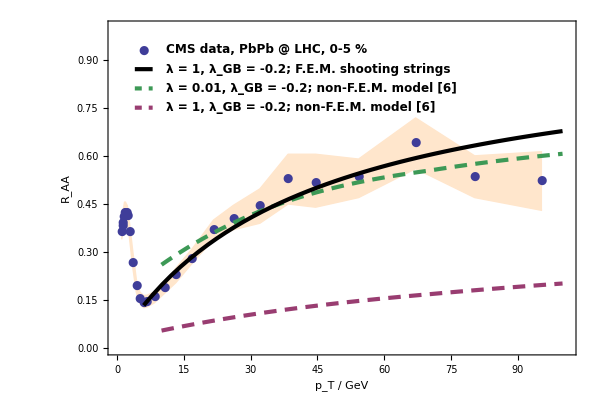

```mathematica
IntroFigForExport=Show[CMSPlot,RAAFall001Plot,RAAFall1Plot,LHCPlot1,LegendsGB]
```

```mathematica
(*Export["MathFigure-IntroFigNew.pdf",IntroFigForExport];*)
```

### RHIC central RAA

#### We will use:

```mathematica
ParamsPlot[2]
ParamsPlot[3]
ParamsPlot[4]
```

RHIC | b = 3, t_i = 1, TrExp = Sqrt, T_freeze = 0.17, κ_temp = 1, ϕ = in | λ = 0.25, CFT-Corr, z_0 = 1

RHIC | b = 3, t_i = 1, TrExp = Sqrt, T_freeze = 0.17, κ_temp = 1, ϕ = in | λ = 3., CFT-Corr, z_0 = 1

RHIC | b = 3, t_i = 1, TrExp = Sqrt, T_freeze = 0.17, κ_temp = 1, ϕ = in | λ = 1., CFT-Corr, z_0 = 1

```mathematica
RHICPlot2=Plot[RAAOpt[2][x/FFRHIC],{x,0,30},PlotStyle->{Thickness[0.005],ColorData[1,6]}];
RHICPlot3Alt=Plot[RAAOpt[3][x/FFRHIC],{x,0,30},PlotStyle->{Thickness[0.005],ColorData[1,4]}];
RHICPlot4=Plot[RAAOpt[4][x/FFRHIC],{x,0,30},PlotStyle->{Thickness[0.005],ColorData[1,3]}];
```

#### Custom legends

```mathematica
LegendsRHICCentral=
{Graphics[Text[Style["λ = 0.25",16,Italic,Bold,Black,FontFamily->"Helvetica"],{11.4,0.6},{-1,0}]],
Graphics[Text[Style["λ = 1",16,Italic,Bold,Black,FontFamily->"Helvetica"],{15.4,0.44},{-1,0}]],
Graphics[Text[Style["λ = 3",16,Italic,Bold,Black,FontFamily->"Helvetica"],{19.4,0.32},{-1,0}]],
Graphics[Text[Style["■",12,ColorData[1,2],FontFamily->"Helvetica"],{5,0.94}]],
Graphics[Text[Style["PHENIX data, AuAu @ RHIC, 0-5%",12,Italic,Bold,Black,FontFamily->"Helvetica"],{5.8,0.94},{-1,0}]]
};
```

#### Combine all

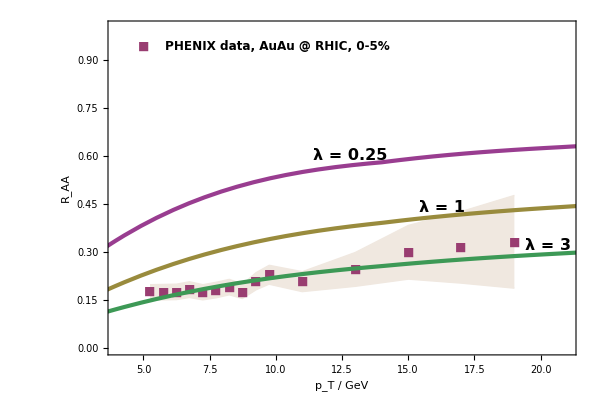

```mathematica
RHICCentralForExport=Show[PHENIXPlot,RHICPlot2,RHICPlot3Alt,RHICPlot4,LegendsRHICCentral]
```

```mathematica
(*Export["MathFigure-RHICCentral.pdf",RHICCentralForExport];*)
```

### LHC central RAA

#### We will use

```mathematica
ParamsPlot[5]
ParamsPlot[6]
ParamsPlot[7]
```

LHC | b = 3, t_i = 1, TrExp = Sqrt, T_freeze = 0.17, κ_temp = 1, ϕ = in | λ = 0.25, CFT-Corr, z_0 = 1

LHC | b = 3, t_i = 1, TrExp = Sqrt, T_freeze = 0.17, κ_temp = 1, ϕ = in | λ = 3., CFT-Corr, z_0 = 1

LHC | b = 3, t_i = 1, TrExp = Sqrt, T_freeze = 0.17, κ_temp = 1, ϕ = in | λ = 1., CFT-Corr, z_0 = 1

```mathematica
LHCPlot5=Plot[RAAOpt[5][x/FFLHC],{x,0,100},PlotStyle->{Thickness[0.005],ColorData[1,6]}];
LHCPlot6=Plot[RAAOpt[6][x/FFLHC],{x,0,100},PlotStyle->{Thickness[0.005],ColorData[1,4]}];
LHCPlot7=Plot[RAAOpt[7][x/FFLHC],{x,0,100},PlotStyle->{Thickness[0.005],ColorData[1,3]}];
```

#### Custom legends

```mathematica
LegendsLHCCentral=
{Graphics[Text[Style["●",12,ColorData[1,1],FontFamily->"Helvetica"],{6,0.93}]],
Graphics[Text[Style["CMS data, PbPb @ LHC, 0-5 %",12,Italic,Bold,Black,FontFamily->"Helvetica"],{11,0.93},{-1,0}]],
Graphics[Text[Style["λ = 0.25",16,Italic,Bold,Black,FontFamily->"Helvetica"],{80,0.69},{-1,0}]],
Graphics[Text[Style["λ = 1",16,Italic,Bold,Black,FontFamily->"Helvetica"],{60,0.445},{-1,0}]],
Graphics[Text[Style["λ = 3",16,Italic,Bold,Black,FontFamily->"Helvetica"],{40,0.25},{-1,0}]]
};
```

#### Combine all

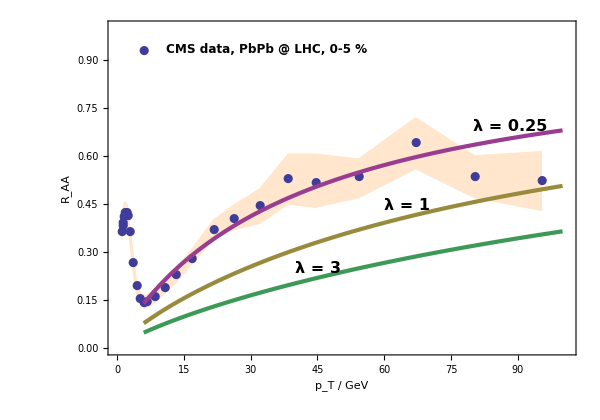

```mathematica
LHCCentralForExport=Show[CMSPlot,LHCPlot5,LHCPlot6,LHCPlot7,LegendsLHCCentral]
```

```mathematica
(*Export["MathFigure-LHCCentral.pdf",LHCCentralForExport];*)
```

### GB vs pureAdS RAA comparison

#### Custom legends

```mathematica
LegendsGBLHC=
{Graphics[Text[Style["●",12,ColorData[1,1],FontFamily->"Helvetica"],{6,0.93}]],
Graphics[Text[Style["CMS data, PbPb @ LHC, 0-5 %",12,Italic,Bold,Black,FontFamily->"Helvetica"],{11,0.93},{-1,0}]],
Graphics[Text[Style["λ = 1, λ_GB = 0",16,Italic,Bold,Black,FontFamily->"Helvetica"],{45,0.3},{-1,0}]],
Graphics[Text[Style["λ = 1, λ_GB = -0.2",16,Italic,Bold,Black,FontFamily->"Helvetica"],{75,0.71},{-1,0}]]
};
```

#### Combine

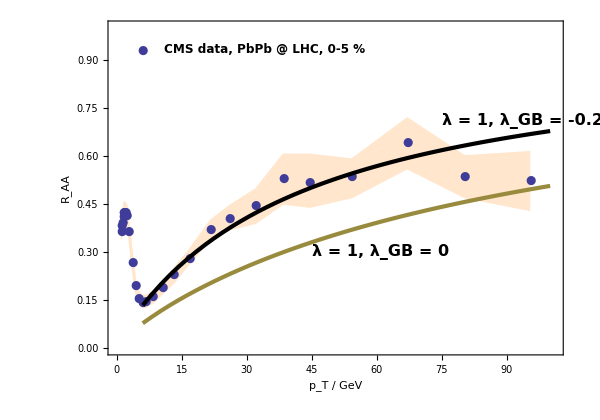

```mathematica
GBCompForExport=Show[CMSPlot,LHCPlot1,LHCPlot7,LegendsGBLHC]
```

```mathematica
(*Export["MathFigure-GBComp.pdf",GBCompForExport];*)
```

### Noncentral RAA for RHIC

#### We choose:

```mathematica
ParamsPlot[3]
ParamsPlot[8]
ParamsPlot[9]
```

RHIC | b = 3, t_i = 1, TrExp = Sqrt, T_freeze = 0.17, κ_temp = 1, ϕ = in | λ = 3., CFT-Corr, z_0 = 1

RHIC | b = 7, t_i = 1, TrExp = Sqrt, T_freeze = 0.17, κ_temp = 1, ϕ = in | λ = 3., CFT-Corr, z_0 = 1

RHIC | b = 7, t_i = 1, TrExp = Sqrt, T_freeze = 0.17, κ_temp = 1, ϕ = out | λ = 3., CFT-Corr, z_0 = 1

#### Plot them

```mathematica
RHICPlot3=Plot[RAAOpt[3][x/FFRHIC],{x,0,30},PlotStyle->{Thickness[0.005],ColorData[1,3]}];
RHICPlot8=Plot[RAAOpt[8][x/FFRHIC],{x,0,30},PlotStyle->{Thickness[0.005],Black}];
RHICPlot9=Plot[RAAOpt[9][x/FFRHIC],{x,0,30},PlotStyle->{Thickness[0.005],ColorData[1,2]}];
```

#### Custom legends

```mathematica
LegendsRHICNoncentral=
{Graphics[Text[Style["■",12,ColorData[1,2],FontFamily->"Helvetica"],{5,0.94}]],
Graphics[Text[Style["PHENIX data, AuAu @ RHIC, 0-5%",12,Italic,Bold,Black,FontFamily->"Helvetica"],{5.8,0.94},{-1,0}]],
Graphics[{Thickness[0.005],ColorData[1,3],Line[{{4.6,0.88},{5.4,0.88}}]}],
Graphics[Text[Style["λ = 3, λ_GB = 0, b = 3 fm",12,Italic,Bold,Black,FontFamily->"Helvetica"],{5.8,0.88},{-1,0}]],
Graphics[Text[Style["▲",14,ColorData[1,4],FontFamily->"Helvetica"],{5,0.82}]],
Graphics[Text[Style["PHENIX data, AuAu @ RHIC, 20-30%, In",12,Italic,Bold,Black,FontFamily->"Helvetica"],{5.8,0.82},{-1,0}]],
Graphics[{Thickness[0.005],Black,Line[{{4.6,0.76},{5.4,0.76}}]}],
Graphics[Text[Style["λ = 3, λ_GB = 0, b = 7 fm, ϕ = 0",12,Italic,Bold,Black,FontFamily->"Helvetica"],{5.8,0.76},{-1,0}]],
Graphics[Text[Style["▼",14,ColorData[1,5],FontFamily->"Helvetica"],{5,0.70}]],
Graphics[Text[Style["PHENIX data, AuAu @ RHIC, 20-30%, Out",12,Italic,Bold,Black,FontFamily->"Helvetica"],{5.8,0.70},{-1,0}]],
Graphics[{Thickness[0.005],ColorData[1,2],Line[{{4.6,0.64},{5.4,0.64}}]}],
Graphics[Text[Style["λ = 3, λ_GB = 0, b = 7 fm, ϕ = π/2",12,Italic,Bold,Black,FontFamily->"Helvetica"],{5.8,0.64},{-1,0}]]
};
```

#### Combine all

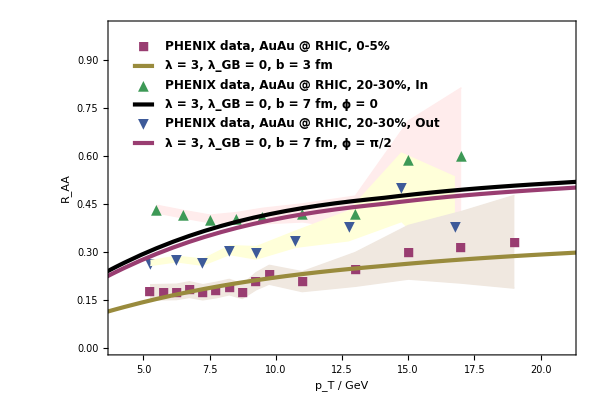

```mathematica
RHICNoncentralForExport=Show[PHENIXAllPlots,RHICPlot3,RHICPlot8,RHICPlot9,LegendsRHICNoncentral]
```

```mathematica
(*Export["MathFigure-RHICnoncentral.pdf",RHICNoncentralForExport];*)
```

### v2 for LHC

#### We choose:

```mathematica
ParamsPlot[10]
ParamsPlot[11]
ParamsPlot[12]
ParamsPlot[13]
```

LHC | b = 7, t_i = 1, TrExp = Sqrt, T_freeze = 0.17, κ_temp = 1, ϕ = in | λ = 1., CFT-GB-Corr, λGB = -0.2, z_0 = 1

LHC | b = 7, t_i = 1, TrExp = Sqrt, T_freeze = 0.17, κ_temp = 1, ϕ = out | λ = 1., CFT-GB-Corr, λGB = -0.2, z_0 = 1

LHC | b = 9, t_i = 1, TrExp = Sqrt, T_freeze = 0.17, κ_temp = 1, ϕ = in | λ = 1., CFT-GB-Corr, λGB = -0.2, z_0 = 1

LHC | b = 9, t_i = 1, TrExp = Sqrt, T_freeze = 0.17, κ_temp = 1, ϕ = out | λ = 1., CFT-GB-Corr, λGB = -0.2, z_0 = 1

#### Construct v2, interpolate and plot

```mathematica
v2Listb7=
Table[{RAAInput[[2*10]][[i,1]]*FFLHC,Abs[RAAInput[[2*10]][[i,2]]-RAAInput[[2*11]][[i,2]]]/(RAAInput[[2*10]][[i,2]]+RAAInput[[2*11]][[i,2]])},{i,1,Length[RAAInput[[2*10]]]}];
v2Listb9=
Table[{RAAInput[[2*12]][[i,1]]*FFLHC,Abs[RAAInput[[2*12]][[i,2]]-RAAInput[[2*13]][[i,2]]]/(RAAInput[[2*12]][[i,2]]+RAAInput[[2*13]][[i,2]])},{i,1,Length[RAAInput[[2*12]]]}];
```

```mathematica
v2Listb7Int=Interpolation[v2Listb7];
v2Listb9Int=Interpolation[v2Listb9];
```

```mathematica
v2PlotLHC=Plot[{v2Listb7Int[pT],v2Listb9Int[pT]},{pT,6,60},PlotStyle->{{Thickness[0.005],ColorData[1,2]},{Thickness[0.005],ColorData[1,3]}},Filling->{1->{2}},PlotRange->{{0,61},{0,0.25}},ImageSize->600,Axes->False,AspectRatio->.7,Frame->True,RotateLabel->True,AxesOrigin->{0,0},LabelStyle->{Directive[Black,12],FontFamily->"Helvetica"},FrameLabel->{Style["p_T / GeV",FontSize->15,Italic,Bold],Style["v_2",FontSize->15,Italic,Bold]},RotateLabel->False];
```

#### Make custom legends

```mathematica
Legendsv2=
{Graphics[Text[Style["●",11,ColorData[1,1],FontFamily->"Helvetica"],{32,0.235}]],
Graphics[Text[Style["CMS data, PbPb @ LHC, 20-30%",13,Italic,Bold,Black,FontFamily->"Helvetica"],{35,0.235},{-1,0}]],
Graphics[{Thickness[0.005],ColorData[1,2],Line[{{31,0.221},{33,0.221}}]}],
Graphics[Text[Style["λ = 1, λ_GB = -0.2, b = 7 fm",13,Italic,Bold,Black,FontFamily->"Helvetica"],{35,0.221},{-1,0}]],
Graphics[{Thickness[0.005],ColorData[1,3],Line[{{31,0.207},{33,0.207}}]}],
Graphics[Text[Style["λ = 1, λ_GB = -0.2, b = 9 fm",13,Italic,Bold,Black,FontFamily->"Helvetica"],{35,0.207},{-1,0}]]
};
```

#### Compare with the data and produce the final plot

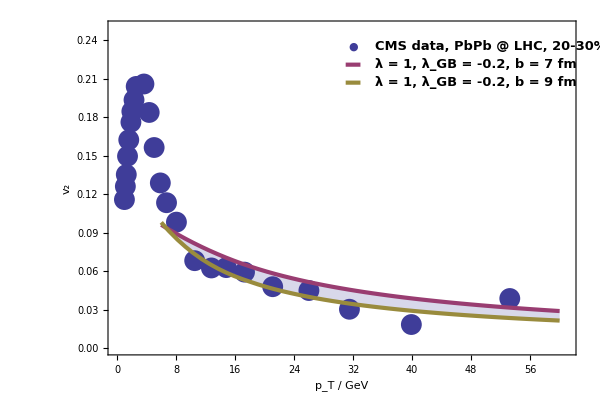

```mathematica
v2LHCForExport=Show[CMSv2Plot,v2PlotLHC,Legendsv2]
```

```mathematica
(*Export["MathFigure-v2LHC.pdf",v2LHCForExport];*)
```

### RHIC Raa temperature comparison

#### We will deal with:

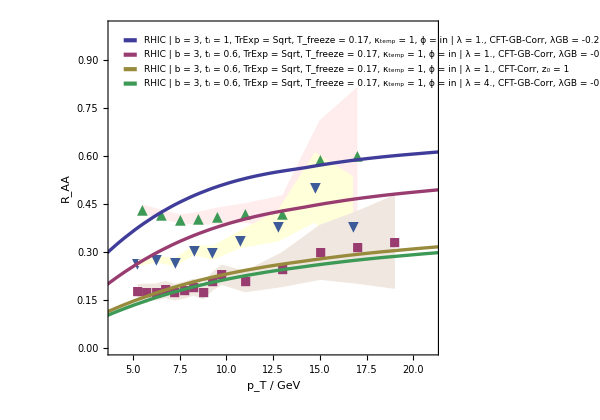

```mathematica
RAARHICOffCentralPlots[{14,15,16,17}]
```

#### Plot what I need

```mathematica
RHICPlot14=Plot[RAAOpt[14][x/FFRHIC],{x,0,30},PlotStyle->{Thickness[0.005],ColorData[1,1]}];
RHICPlot15=Plot[RAAOpt[15][x/FFRHIC],{x,0,30},PlotStyle->{Thickness[0.005],ColorData[1,2]}];
RHICPlot16=Plot[RAAOpt[16][x/FFRHIC],{x,0,30},PlotStyle->{Thickness[0.005],ColorData[1,3]}];
RHICPlot17=Plot[RAAOpt[17][x/FFRHIC],{x,0,30},PlotStyle->{Thickness[0.005],ColorData[1,4]}];
```

#### Custom legends

```mathematica
LegendsRHICExtra={
Graphics[Text[Style["■",12,ColorData[1,2],FontFamily->"Helvetica"],{5,0.94}]],
Graphics[Text[Style["PHENIX data, AuAu @ RHIC, 0-5%",12,Italic,Bold,Black,FontFamily->"Helvetica"],{5.8,0.94},{-1,0}]],
Graphics[{Thickness[0.006],ColorData[1,1],Line[{{4.7,0.94-1*0.06},{5.3,0.94-1*0.06}}]}],
Graphics[Text[Style["λ = 1, λ_GB = -0.2, t_i = 1 fm/c",12,Italic,Bold,Black,FontFamily->"Helvetica"],{5.8,0.94-1*0.06},{-1,0}]],
Graphics[{Thickness[0.006],ColorData[1,2],Line[{{4.7,0.94-2*0.06},{5.3,0.94-2*0.06}}]}],
Graphics[Text[Style["λ = 1, λ_GB = -0.2, t_i = 0.6 fm/c",12,Italic,Bold,Black,FontFamily->"Helvetica"],{5.8,0.94-2*0.06},{-1,0}]],
Graphics[{Thickness[0.006],ColorData[1,3],Line[{{4.7,0.94-3*0.06},{5.3,0.94-3*0.06}}]}],
Graphics[Text[Style["λ = 1, λ_GB = 0, t_i = 0.6 fm/c",12,Italic,Bold,Black,FontFamily->"Helvetica"],{5.8,0.94-3*0.06},{-1,0}]],
Graphics[{Thickness[0.006],ColorData[1,4],Line[{{4.7,0.94-4*0.06},{5.3,0.94-4*0.06}}]}],
Graphics[Text[Style["λ = 4, λ_GB = -0.2, t_i = 0.6 fm/c",12,Italic,Bold,Black,FontFamily->"Helvetica"],{5.8,0.94-4*0.06},{-1,0}]]
};
```

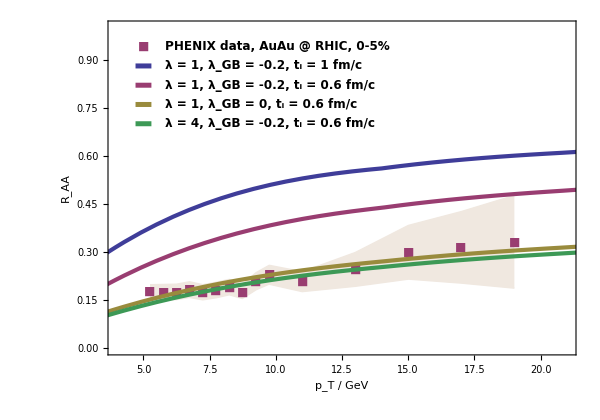

```mathematica
RHICTempForExport=Show[PHENIXPlot,RHICPlot14,RHICPlot15,RHICPlot16,RHICPlot17,LegendsRHICExtra]
```

```mathematica
(*Export["MathFigure-RHICTemp.pdf",RHICTempForExport];*)
```

### LHC temperature comparison

#### We will deal with

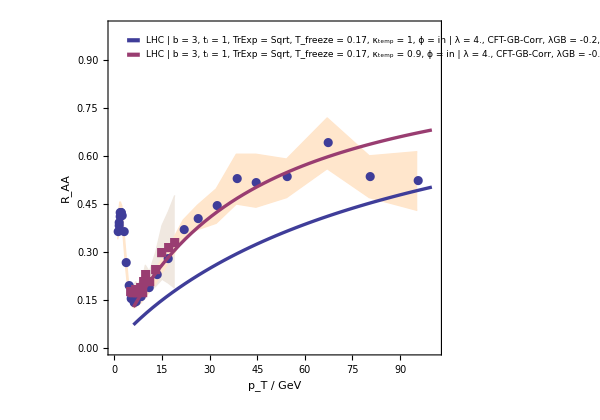

```mathematica
RAACentralPlots[{18,19}]
```

#### Plot what we need

```mathematica
LHCPlot18=Plot[RAAOpt[18][x/FFLHC],{x,0,100},PlotStyle->{Thickness[0.005],ColorData[1,1]}];
LHCPlot19=Plot[RAAOpt[19][x/FFLHC],{x,0,100},PlotStyle->{Thickness[0.005],ColorData[1,2]}];
```

#### Custom legends

```mathematica
RAACentralPlots[list_]:=Show[JoinedCMSPHENIX,
Plot[Evaluate[Table[If[ParamsCase[i][[5]]=="LHC",RAAOpt[i][x/FFLHC],RAAOpt[i][x/FFRHIC]],{i,list}]],{x,0,100},PlotStyle->Thickness[0.004]],
Table[Graphics[Text[Style[ParamsPlot[list[[i]]],9,Italic,Black,FontFamily->"Helvetica"],
{10,0.96-(i-1)*0.045},{-1,0}]],{i,1,Length[list]}],
Table[Graphics[{Thickness[0.005],ColorData[1,i],
Line[{{4,0.96-(i-1)*0.045},{8,0.96-(i-1)*0.045}}]}],{i,1,Length[list]}]];
```

```mathematica
LegendsLHCTemp={
Graphics[Text[Style["●",12,ColorData[1,1],FontFamily->"Helvetica"],{6,0.93}]],
Graphics[Text[Style["CMS data, PbPb @ LHC, 0-5 %",12,Italic,Bold,Black,FontFamily->"Helvetica"],{11,0.93},{-1,0}]],
Graphics[{Thickness[0.006],ColorData[1,1],Line[{{4,0.93-1*0.06},{8,0.93-1*0.06}}]}],
Graphics[Text[Style["λ = 4, λ_GB = -0.2, t_i = 1 fm/c, κ = 1",12,Italic,Bold,Black,FontFamily->"Helvetica"],{11,0.93-1*0.06},{-1,0}]],
Graphics[{Thickness[0.006],ColorData[1,2],Line[{{4,0.93-2*0.06},{8,0.93-2*0.06}}]}],
Graphics[Text[Style["λ = 4, λ_GB = -0.2, t_i = 1 fm/c, κ = 0.9",12,Italic,Bold,Black,FontFamily->"Helvetica"],{11,0.93-2*0.06},{-1,0}]]
};
```

#### Plot and export

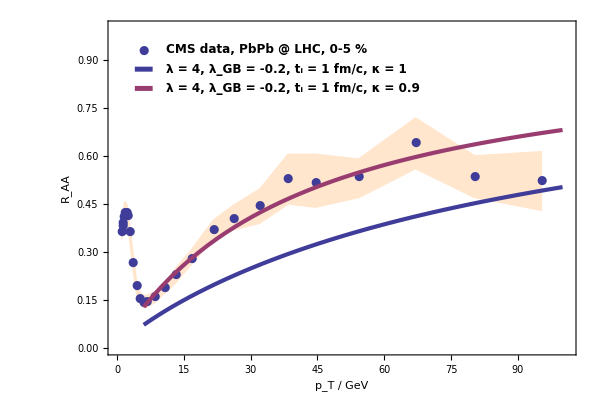

```mathematica
LHCTempForExport=Show[CMSPlot,LHCPlot18,LHCPlot19,LegendsLHCTemp]
```

```mathematica
(*Export["MathFigure-LHCTemp.pdf",LHCTempForExport];*)
```